```mathematica
profit= Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\Dataset\\profit q=1.5 k=80.csv"]];
mm2 = profit[[1]];
mm3 = profit[[2]];
mm2 = Delete[mm2,1];
mm3 = Delete[mm3,1];
FindDistributionParameters[mm3,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[mm3,NormalDistribution[μ, σ]]
```

{μ→1.53184,β→1.16897,q→1.4785}

{μ→1.53184,σ→2.29086}

```mathematica
Skewness[mm2]
Skewness[mm3]
```

2.99718

3.17821

```mathematica
FindDistributionParameters[mm2,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[mm2,NormalDistribution[μ, σ]]
```

{μ→1.01464,β→0.0394308,q→1.51162}

{μ→1.01464,σ→0.097895}

```mathematica
FindDistributionParameters[mm2,TsallisQGaussianDistribution[μ,β,q]]
```

{μ→2.24896,β→0.196524,q→1.10589}

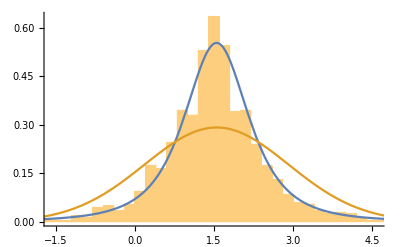

```mathematica
Show[Histogram[mm3,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[1.549,0.55,1.58],x],PDF[NormalDistribution[1.549,1.367],x]},{x,-2,5}]]
```

```mathematica
TsallisVar[μ_, β_, q_] :=Variance[TsallisQGaussianDistribution[μ,β,q]]
NormalVar[μ_, σ_]:=Variance[NormalDistribution[μ,σ]]


TsallisDrift[μ_, β_,q_]:=μ+TsallisVar[μ, β, q]/2
NormalDrift[μ_,σ_]:=μ+NormalVar[μ, σ]/2
TsallisVolatility[μ_,β_, q_]:=√TsallisVar[μ, β, q]
NormalVolatility[μ_,σ_]:=√NormalVar[μ, σ]
```

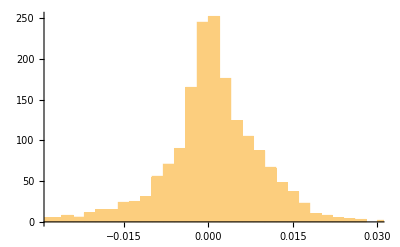

```mathematica
Histogram[return]
```

```mathematica
p =Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\SatT.csv"]];
p =p[[2]];
p = Delete[p, 1];
```

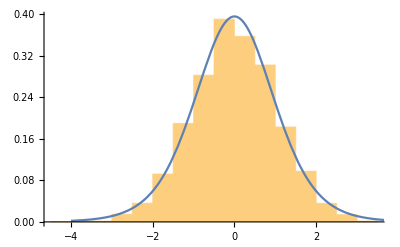

```mathematica
Show[Histogram[p,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[0.00039,0.931032512,1.2],x]},{x,-4,4}]]
```

```mathematica
profit= Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\3 profits dists.csv"]];
mm2 = profit[[1]];
mm3 = profit[[2]];
mm4 = profit[[3]];
mm2 = Delete[mm2,1];
mm3 = Delete[mm3,1];
mm4 = Delete[mm4,1];
FindDistributionParameters[mm4,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[mm4,NormalDistribution[μ, σ]]
```

{μ→1.01545,β→0.720073,q→1.51285}

{μ→1.01545,σ→1.37717}

```mathematica
FindDistributionParameters[mm2,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[mm2,NormalDistribution[μ, σ]]
```

{μ→0.993629,β→0.723341,q→1.00793}

{μ→0.993629,σ→0.727681}

```mathematica
FindDistributionParameters[mm4,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[mm4,NormalDistribution[μ, σ]]
```

{μ→1.00926,β→0.789598,q→1.41958}

{μ→1.00926,σ→1.25931}

```mathematica
Skewness[mm2]
```

0.0265143

```mathematica
Skewness[mm3]
```

0.134487

```mathematica
Skewness[mm4]
```

0.460209

```mathematica
JarqueBeraALMTest[mm2]
```

0.925767

```mathematica
JarqueBeraALMTest[mm3]
```

0

```mathematica
JarqueBeraALMTest[mm4]
```

0